# Fig1 and 2

## code for band dispersion and phase diagram calculation

#### geo

```mathematica
a1={Sqrt[3]/2,-1/2};a2={Sqrt[3]/2,1/2};
b6={2*Pi/Sqrt[3],-2*Pi};b2={2*Pi/Sqrt[3],2*Pi};
Simplify[a1.b6];
Simplify[a2.b6];
Simplify[a1.b2];
Simplify[a2.b2];
kG={0,0}.{b6,b2};
kM={0,1/2}.{b6,b2};
kK={1/3,2/3}.{b6,b2};
```

```mathematica
kM
```

{π/(√3),π}

```mathematica
kK//Norm
```

(4 π)/3

```mathematica
a1//Norm
```

1

```mathematica
a1.b3
```

{(√3)/2,-1/2}.b3

```mathematica
a1.b2
```

0

```mathematica
a2.b
```

{(√3)/2,1/2}.b

```mathematica
b1=b6+b2;b4=-b1;b3=-b6;b5=-b2;
```

```mathematica
b={b1,b2,b3,b4,b5,b6};
```

```mathematica
gg2[ θ_]:=(θ 4π)/(√3){(√3)/2,-1/2};gg3[ θ_]:=(θ 4π)/(√3){(√3)/2,1/2};gg1 [ θ_]=gg2[ θ]-gg3[ θ];gg4[ θ_]:=-gg1[ θ];gg5[ θ_]=-gg2[ θ];gg6[ θ_]=-gg3[ θ];
```

```mathematica
bb={b2+b3,b3+b4,b4+b5,b5+b6,b6+b1,b1+b2}
```

{{0,4 π},{-2 √3 π,2 π},{-2 √3 π,-2 π},{0,-4 π},{2 √3 π,-2 π},{2 √3 π,2 π}}

```mathematica
{gg1[1],gg2[1],gg3[1],gg4[1],gg5[1],gg6[1]}
```

{{0,-(4 π)/(√3)},{2 π,-(2 π)/(√3)},{2 π,(2 π)/(√3)},{0,(4 π)/(√3)},{-2 π,(2 π)/(√3)},{-2 π,-(2 π)/(√3)}}

```mathematica
TA=5Pi/180;
```

```mathematica
gg2[TA]//Norm
```

π^2/(9 √3)

#### Hamiltonian

```mathematica
A=0.365;B=-0.706;D2=-0.532
```

-0.532

```mathematica
HBHZ[{kx_,ky_},M_]:=A( kx PauliMatrix[1]- ky PauliMatrix[2]) +(M-B(kx^2+ky^2)) PauliMatrix[3]-D2(kx^2+ky^2) PauliMatrix[0]
```

```mathematica
HBHZT[{kx_,ky_},M_]:=BlockDiagonalMatrix[{HBHZ[{kx,ky},M],HBHZ[-{kx,-ky},M]}]+10 IdentityMatrix[4]//Normal
```

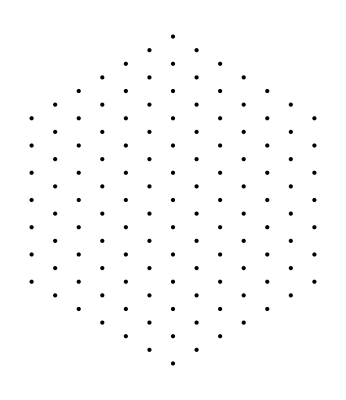

```mathematica
n=6;Glength=Join[Table[i,{i,n+1,2n}],{2n+1},Table[i,{i,2n,n+1,-1}]];Gbegin=Table[Total@Glength[[1;;i]]-Glength[[i]]+1,{i,1,Length[Glength]}];G[θ_]:=Join[ArrayFlatten[Table[(n-i)gg5[ θ]+j gg1[ θ],{i,0,n},{j,-i,n}],1],ArrayFlatten[Table[(-i)gg5[ θ]+j gg1[ θ],{i,1,n},{j,-n,n-i}],1]];Graphics[Point[G[1]]]
```

```mathematica
HBHZT[{kx,ky}+G[TA][[1]],M]
```

{{10.+M+1.238 ((kx-π^2/3)^2+(ky+π^2/(3 √3))^2),0.+0.365 (kx-π^2/3+ⅈ (ky+π^2/(3 √3))),0,0},{0.+0.365 (kx-π^2/3-ⅈ (ky+π^2/(3 √3))),10.-M-0.174 ((kx-π^2/3)^2+(ky+π^2/(3 √3))^2),0,0},{0,0,10.+M+1.238 ((-kx+π^2/3)^2+(ky+π^2/(3 √3))^2),0.+0.365 (-kx+π^2/3+ⅈ (ky+π^2/(3 √3)))},{0,0,0.+0.365 (-kx+π^2/3-ⅈ (ky+π^2/(3 √3))),10.-M-0.174 ((-kx+π^2/3)^2+(ky+π^2/(3 √3))^2)}}

```mathematica
HInt=Normal@BlockDiagonalMatrix@ParallelTable[ HBHZT[{kx,ky}+G[TA][[i]],M],{i,1,Total@Glength}];
```

```mathematica
diagH[{kxx_,kyy_},dd_]:=N@Chop@HInt/.{kx->kxx,ky->kyy,M->dd}
```

```mathematica
{off1=ConstantArray[0,{Total@Glength,Total@Glength}];Table[off1[[i,i+1]]=1;,{j,1,2n+1},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-2}];}
```

{Null}

```mathematica
{off2=ConstantArray[0,{Total@Glength,Total@Glength}];
Table[off2[[i,i+Glength[[j]]+1]]=1;,{j,1,n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-1}];
Table[off2[[i,i+Glength[[j]]]]=1;,{j,n+1,2n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-2}];}
```

{Null}

```mathematica
{off3=ConstantArray[0,{Total@Glength,Total@Glength}];
Table[off3[[i,i+Glength[[j]]]]=1;,{j,1,n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-1}];
Table[off3[[i,i+Glength[[j]]-1]]=1;,{j,n+1,2n},{i,Gbegin[[j]]+1,Gbegin[[j]]+Glength[[j]]-1}];}
```

{Null}

```mathematica
Hinterationn[V_]:=DiagonalMatrix[{0V,V,0V,V}];diaH[V_]:=Chop@N@KroneckerProduct[off1+off2+off3+Transpose@off1+Transpose@off2+Transpose@off3,Hinterationn[V]]
```

```mathematica
TotalHam3[{kx_,ky_},m_,V_]:=Chop[N[diagH[{kx,ky},m]+diaH[V]]];
```

```mathematica
dim=Dimensions[TotalHam3[{0,0},0.5,0]][[1]]
```

508

```mathematica
rang=Flatten[Table[4j+i,{j,0,Total[Glength]-1},{i,1,2}]];
```

```mathematica
um0=Table[0,{i,1,dim}];
```

```mathematica
UM=Table[ReplacePart[um0,i->1],{i,rang}];
```

```mathematica
HIntHalf=UM.TotalHam3[{kx,ky},m,v].Transpose[UM];
```

```mathematica
TotalHam3half[{kxx_,kyy_},mm_,vv_]:=HIntHalf/.{kx->kxx,ky->kyy,m->mm,v->vv};
```

#### dispersion and phase diagram

```mathematica
M0=0.135;v0=0.089;
```

```mathematica
mkK= {TA 4 π/3, 0};mkM=TA{π,-π/(√3)};mkG={0,0};
```

```mathematica
temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4-4,dim/4+4}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p10=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Black,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,GridLines->{{101,201},{}},FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black],GridLinesStyle->Directive[Black]];temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4+1}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p11=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Red,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black]];
```

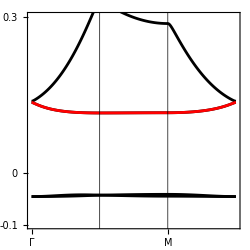

```mathematica
Show[{p10,p11},ImageSize->250,PlotRange->{-0.1,0.3},Framed->True,FrameTicksStyle->{FontSize->20,FontWeight->"Bold",FontFamily->"Times"},BaseStyle->{FontSize->20,FontWeight->"Bold"}]
```

```mathematica
M0=0.135;v0=0.094;
```

```mathematica
temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4-4,dim/4+4}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p10=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Black,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,GridLines->{{101,201},{}},FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black],GridLinesStyle->Directive[Black]];temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4+1}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p11=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Red,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black]];
```

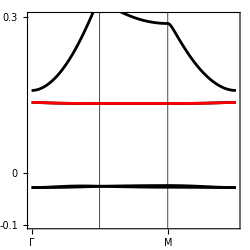

```mathematica
Show[{p10,p11},ImageSize->250,PlotRange->{-0.1,0.3},Framed->True,FrameTicksStyle->{FontSize->20,FontWeight->"Bold",FontFamily->"Times"},BaseStyle->{FontSize->20,FontWeight->"Bold"}]
```

```mathematica
M0=0.135;v0=0.054;
```

```mathematica
temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4-4,dim/4+4}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p10=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Black,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,GridLines->{{101,201},{}},FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black],GridLinesStyle->Directive[Black]];temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4+1}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p11=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Red,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black]];
```

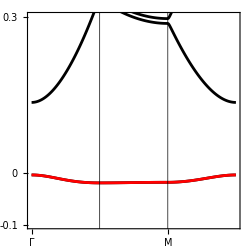

```mathematica
Show[{p10,p11},ImageSize->250,PlotRange->{-0.1,0.3},Framed->True,FrameTicksStyle->{FontSize->20,FontWeight->"Bold",FontFamily->"Times"},BaseStyle->{FontSize->20,FontWeight->"Bold"}]
```

```mathematica
numk=30;B1=gg2[TA];B2=gg3[TA];
```

```mathematica
kspace=Flatten[Table[x/numk B1+y/numk B2,{x,0,numk},{y,0,numk}],1]//DeleteDuplicates//N;
```

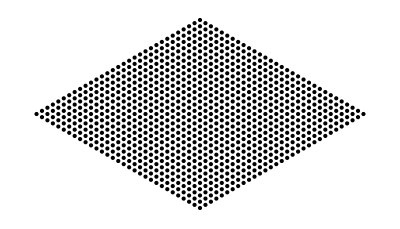

```mathematica
Graphics@Point@kspace
```

```mathematica
gapandw[{m_,v_}]:=Transpose@ParallelTable[Eigenvalues[TotalHam3half[k,m,v],{dim/4-(0-1)-1,dim/4-(0-1)+1}],{k,kspace}];
```

```mathematica
Getgapandw[t_List]:=With[{t1=t[[1]],t2=t[[2]],t3=t[[3]]},{Min[t1-t2],Min[t2-t3],Max[t2]-Min[t2]}]
```

```mathematica
num2=70
```

70

```mathematica
parameterspace=Flatten[Table[{M,v},{v,0.0005,0.1,0.1/num2},{M,-0.07,0.12,0.12/num2}],1];
```

```mathematica
Result=Map[Getgapandw,Table[gapandw[para],{para,parameterspace}]]
```

```mathematica
parameterspacelarge=Flatten[Table[{M,v},{v,0.0005,0.12,0.1/num2},{M,-0.07,0.14,0.12/num2}],1];
```

```mathematica
parameterspaceaddition2=Complement[parameterspacelarge,parameterspace];
```

```mathematica
Resultaddition2=Map[Getgapandw,Table[gapandw[para],{para,parameterspaceaddition2}]];
```

```mathematica
parameterspaceall2=Join[parameterspace,parameterspaceaddition2];
```

```mathematica
Resultall2=Join[Result,Resultaddition2];
```

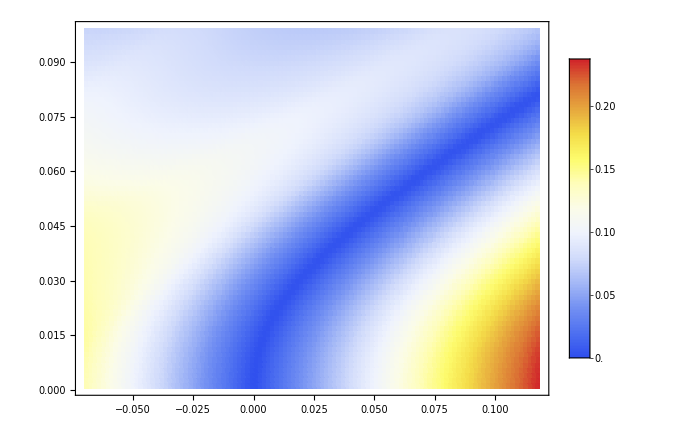

```mathematica
ListDensityPlot[Map[Flatten,Transpose[{parameterspace,Result[[;;,1]]}]],ColorFunction->"TemperatureMap", ImageSize ->Large,PlotLegends->Automatic,InterpolationOrder->All,AspectRatio ->3/4,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[15,Black],LabelStyle->Directive[20,Black]]
```

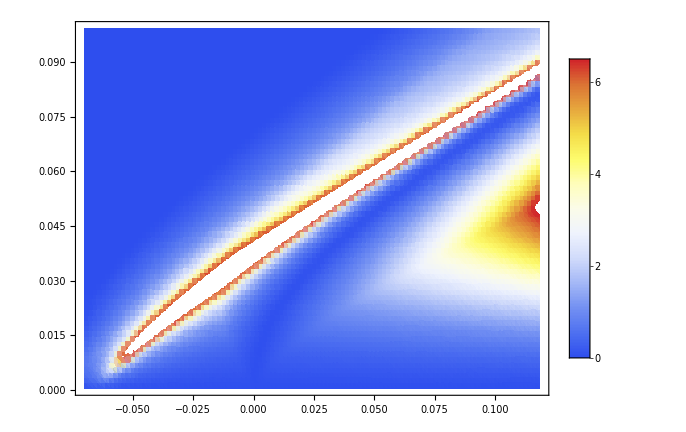

```mathematica
ListDensityPlot[Map[Flatten,Transpose[{parameterspace,Map[Min,Transpose@{Result[[;;,1]],Result[[;;,2]]}]/Result[[;;,3]]}]],ColorFunction->"TemperatureMap", ImageSize ->Large,PlotLegends->Automatic,InterpolationOrder->All,AspectRatio ->3/4,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[15,Black],LabelStyle->Directive[20,Black]]
```

```mathematica
pphase=Map[Flatten,Transpose[{parameterspaceall2,Map[Min,Transpose@{Resultall2[[;;,1]],Resultall2[[;;,2]]}]/Resultall2[[;;,3]]}]];
```

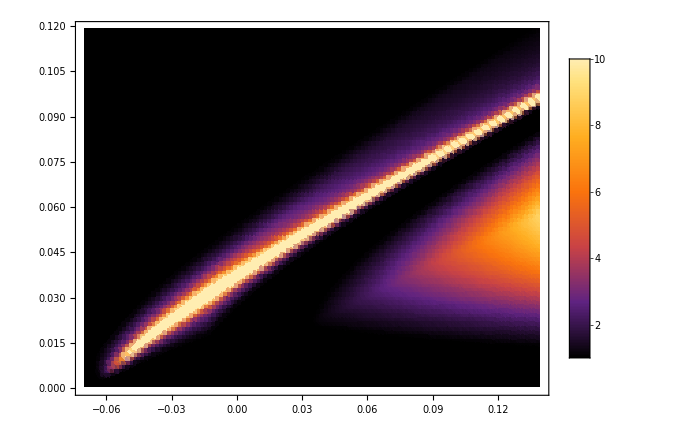

```mathematica
PWDD=ListDensityPlot[pphase,ColorFunction->(ColorData["SunsetColors"]@(0.9*Rescale[#,{1,10}])&),ColorFunctionScaling->False, ImageSize ->Large,PlotLegends->Automatic,InterpolationOrder->All,AspectRatio ->3/4,FrameTicksStyle->Directive[Black,15],LabelStyle->Directive[15,Black],PlotRange->{1,10},ClippingStyle->Automatic]
```

```mathematica
(*phase transition line*)
```

```mathematica
select[a_]:=If[a<=0.00006,-0.01,a]
```

```mathematica
p1=ListContourPlot[Map[Flatten,Transpose[{parameterspaceall2,Map[select,Chop@Resultall2[[;;,2]]]}]],Contours->{0},ContourShading->None,ContourStyle->{{Opacity[1],White,Thickness[0.01/1.5],Dashed}}];
```

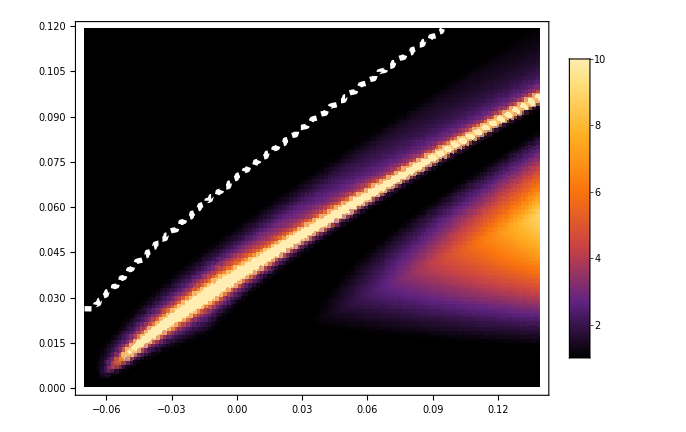

```mathematica
Show[PWDD,p1]
```

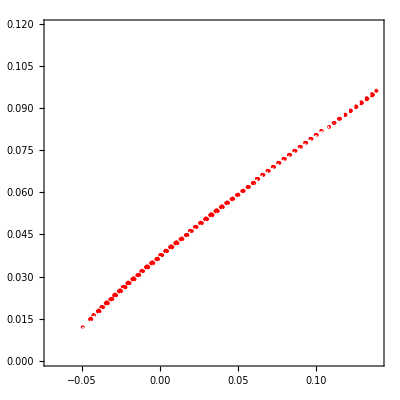

```mathematica
p12=ListContourPlot[Map[Flatten,Transpose[{parameterspaceall2,Resultall2[[;;,3]]}]],Contours->{0.0012},ContourShading->None,ContourStyle->{{Opacity[1],Red,Thickness[0.01/1.5],Dashed}}]
```

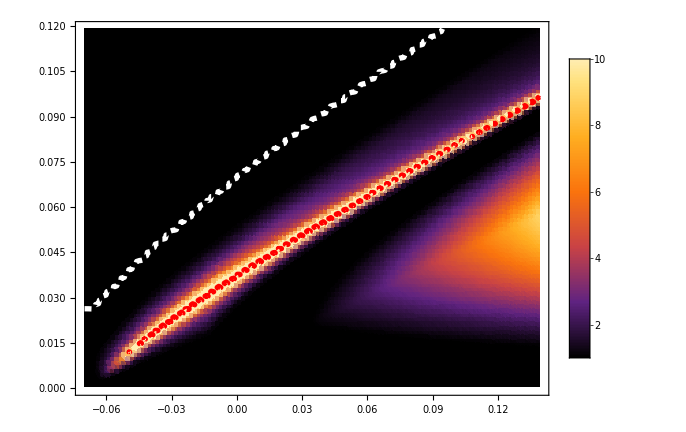

```mathematica
Show[PWDD,p1,p12]
```

```mathematica
ESG[n_,M_,v_]:=Eigensystem[TotalHam3[{0,0},M,v],{dim/2-2(n-1)-1,dim/2-2(n-1)}];
```

```mathematica
c6=DiagonalMatrix[Table[Exp[-I 2Pi/6 j],{j,1/2,3/2}]]
```

{{ⅇ^(-(ⅈ π)/6),0},{0,-ⅈ}}

```mathematica
C6=Normal@BlockDiagonalMatrix@{c6,Conjugate@c6}
```

{{ⅇ^(-(ⅈ π)/6),0,0,0},{0,-ⅈ,0,0},{0,0,ⅇ^((ⅈ π)/6),0},{0,0,0,ⅈ}}

```mathematica
P=KroneckerProduct[IdentityMatrix[2],DiagonalMatrix[{1,-1}]]
```

{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}}

```mathematica
Gforoff=FullSimplify@G[1];zero4=Table[0,{i,1,4},{j,1,4}];c6m[i_,j_]:=If[Gforoff[[i]]==RotationMatrix[2Pi/6].Gforoff[[j]],C6,zero4];C6m=ArrayFlatten@Table[c6m[i,k],{i,1,Total@Glength},{k,1,Total@Glength}];pm[i_,j_]:=If[Gforoff[[i]]==-Gforoff[[j]],P,zero4];Pm=ArrayFlatten@Table[pm[i,k],{i,1,Total@Glength},{k,1,Total@Glength}];
```

```mathematica
C6E[a_]:=Which[Abs[a]<=0.01,1,Abs[a-N[Exp[I 5Pi/6]+Exp[-I 5Pi/6]]]<=0.01,2,Abs[a-N[Exp[I 1Pi/6]+Exp[-I 1Pi/6]]]<=0.01,3];
```

```mathematica
EBRG[{a_,b_}]:=Which[a==3&&Sign[b]==-1,12,a==2&&Sign[b]==-1,11,a==1&&Sign[b]==-1,10,a==3&&Sign[b]==1,9,a==2&&Sign[b]==1,8,a==1&&Sign[b]==1,7];
```

```mathematica
EBRGa[n_,{M_,v_}]:=With[{t=ESG[n,M,v]},{M,v,EBRG@{C6E@Chop@Tr[Conjugate[t[[2]]].C6m.Transpose[t[[2]]]],Chop@Tr[Conjugate[t[[2]]].Pm.Transpose[t[[2]]]]}}]
```

```mathematica
GAchaneg=ParallelTable[EBRGa[0,p],{p,parameterspace}];
```

```mathematica
EBRGa[0,parameterspace[[1]]]
```

{-0.07,0.0005,9}

```mathematica
GAchaneg=ParallelTable[EBRGa[0,p],{p,parameterspace}];
GAchanegaddition2=ParallelTable[EBRGa[0,p],{p,parameterspaceaddition2}];GAchanegadditionall=Join[GAchaneg,GAchanegaddition2];
```

```mathematica
Select2[{a_,b_,c_}]:=If[a>=-0.05,{a,b,c},Null];
```

```mathematica
p20=ListContourPlot[DeleteCases[Map[Select2,GAchanegadditionall],Null],Contours->{9.5},ContourShading->None,ContourStyle->{{Opacity[1],White,Thickness[0.01/1.5],Dashed}},PlotRange->{{-0.05,0.12},{0,0.1}}];
```

```mathematica
PPGMK[{a_,b_},c_]:=Graphics[{Thickness[0.1/20],Green,Opacity[1],Line[{{a,b}+c{1,1},{a,b}-c{1,1}}],Line[{{a,b}+c{-1,1},{a,b}-c{-1,1}}]}];PPGMK2[{a_,b_},c_]:=Graphics[{Thickness[0.1/20],Yellow,Opacity[1],Line[{{a,b}+c{1,1},{a,b}-c{1,1}}],Line[{{a,b}+c{-1,1},{a,b}-c{-1,1}}]}];
```

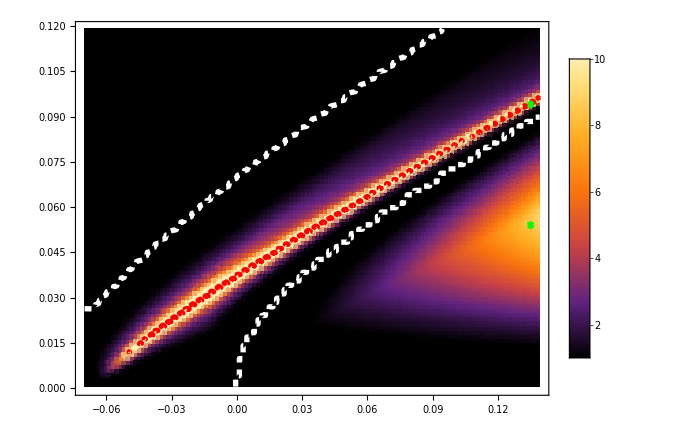

```mathematica
Show[PWDD,p1,p20,p12,PPGMK[{0.135,0.094},0.001],PPGMK[{0.135,0.054},0.001]]
```